y^2=x^3+x+3 (mod p)

3 mod p+x+x^3

Необходимо найти точки y^2=x^3+ax+b(mod p)при p =7

```mathematica
VarsX=Mod[x^3+x+3,7]/.{x->{0,1,2,3,4,5,6}}
```

{3,5,6,5,1,0,1}

```mathematica
VarsY=Mod[y^2,7]/.{y->{0,1,2,3,4,5,6}}
```

{0,1,4,2,2,4,1}

```mathematica
{{5,0},{4,1},{6,1},{4,6},{6,6}};
```

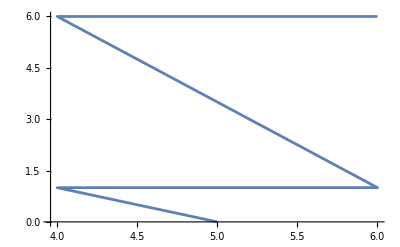

```mathematica
ListLinePlot[{{5,0},{4,1},{6,1},{4,6},{6,6}}]
```

```mathematica
VarsX2=Mod[x^3+2*x,11]/.{x->{0,1,2,3,4,5,6}}
```

{0,3,1,0,6,3,8}

```mathematica
VarsY2=Mod[y^2,11]/.{y->{0,1,2,3,4,5,6}}
```

{0,1,4,9,5,3,3}

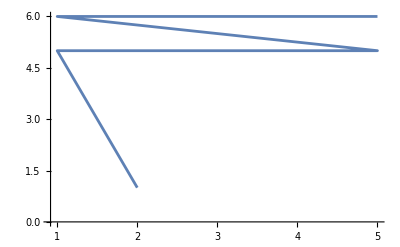

```mathematica
ListLinePlot@{{2,1},{1,5},{5,5},{1,6},{5,6}}
```

```mathematica
m[xp_,yp_,a_]:=(3*xp+a)/(2*yp);
```

```mathematica
m[0,2,3]
```

3/4

```mathematica
m=3*4^-1 mod 7
4x=7k+1
3*2mod 7 = 6
x2p=(m^2-2xp)mod 7
```

```mathematica
x2p[xp_,m_]:=Mod[m^2-2xp,7]
```

```mathematica
x2p[0,6]
```

1

```mathematica
y2p=6
2p=(1,6)
```